```mathematica
xn[a_,b_,g_,n_]:=(a 3^(n+1)+b 5^(n+1)+g 100^(n+1))/(a 3^n+b 5^n+g 100^n)
abg[x0_,x1_]:=FindInstance[x0==xn[a,b,g,0]&&x1==xn[a,b,g,1],{a,b,g}]//N
Lim[x0_,x1_]:=If[-10^-10<x0<10^-10||-10^-10<x1<10^-10,0.,Limit[xn[a,b,g,10]/.abg[x0,x1],n->+∞][[1]]//N]
(*data=Table[Lim[x0,x1],{x0,1,10},{x1,1,10}];*)
s=OpenWrite["/home/kevin/UBA/metnum/metnum2010/trunk/tp1/math.out"];
SetOptions[s,FormatType->TextForm];
For[x0=-10,x0≤10,x0+=.25,For[x1=-10,x1≤10,x1+=.25,
WriteString[s,Chop[x0]," ",Chop[x1]," " ,Lim[x0,x1]//N,"\n"]
]]Close[s];
(*ListPlot3D[data,Mesh->All]
Table[Lim[x0,x1],{x0,1,10},{x1,1,10}]//N;*)
```

```mathematica
f[x_,y_]:=Piecewise[{{3, x==3&&y==3}, {5, (y-8) x+15==0}, {100, True}}]
```

```mathematica
Show[{ParametricPlot3D[{t,-15/t+8,3},{t,-20,20}],Plot3D[100,{x,-20,20},{y,-15,25}],ContourPlot3D[(x-3)^2+(y-3)^2+(z-3)^2==.5,{x,-20,20},{y,-15,25},{z,0,110}]},PlotRange->{{-20,20},{-15,25},{0,110}},BoxRatios->{1,1,.2}]
```

-Graphics3D-

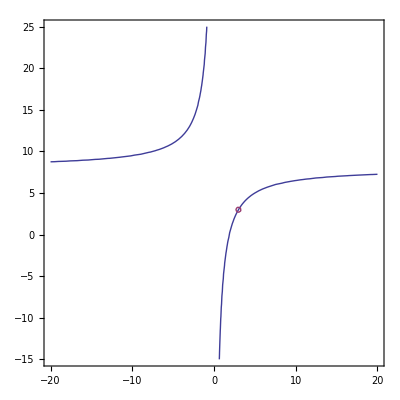

```mathematica
ContourPlot[{(y-8) x+15==0,(x-3)^2+(y-3)^2==.1},{x,-20,20},{y,-15,25}]
```